```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\critical_region\cheby\LPA\v4\scaling\initial_v1\anum21\mub0Tc\buffer

```mathematica
list0=Flatten[Import["a.dat"]];
list=Flatten[Import["b.dat"]];
dataTaylor=Import["../../../../../../mub0data.dat"];
```

```mathematica
list1=Rest[list0];
list2=Rest[list];
```

```mathematica
ρmin=0.;
ρmax=30000.;
c0=1.85*10^6;
fpi=93.5;
cmax=10.^7;
cmin=10.^-2;
```

```mathematica
eqn6=Table[Evaluate[(test=SetPrecision[Sum[list2[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,20}]+1/2 First[list]-Exp[c]*(2ρ)^(-1/2),100])]==0,{c,Log[cmin],Log[cmax],(Log[cmax]-Log[cmin])/100}];
```

```mathematica
res6=Re[Flatten[ParallelMap[FindRoot[#,{ρ,1},WorkingPrecision->98]&,eqn6]][[All,2]]];
```

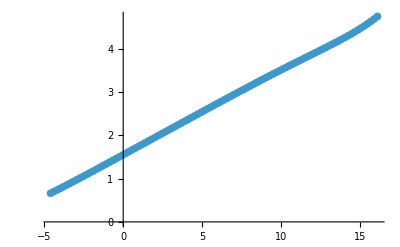

```mathematica
ListLinePlot[data6=Transpose[{Table[Log[Exp[c]],{c,Log[cmin],Log[cmax],(Log[cmax]-Log[cmin])/100}],Log[Sqrt[res6*2]]}],Mesh->All]
```

```mathematica
fit6=LinearModelFit[data6,x,x];
```

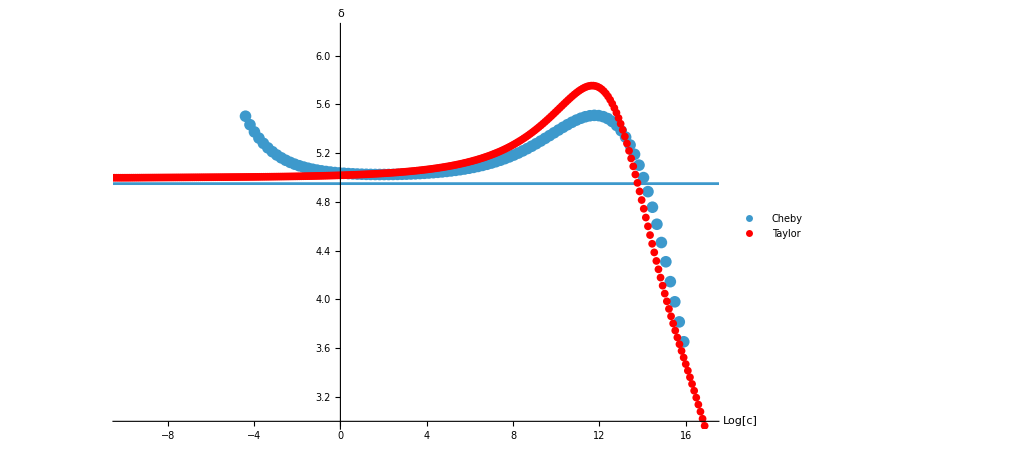

```mathematica
Show[ListPlot[Table[fit6=LinearModelFit[data6[[n;;n+2]],x,x];
{data6[[n;;n+2]][[All,1]]//Mean,1/Normal[fit6][[2]][[1]]},{n,1,Length[data6]-2}],PlotRange->{{-10,17},{3,6.2}},PlotLegends->{"Cheby"}],ListLinePlot[{{-20,4.95},{20,4.95}}],ListPlot[dataTaylor,PlotStyle->Red,PlotLegends->{"Taylor"}],AxesLabel->{"Log[c]","δ"}]
```

```mathematica
eqn6=Table[Evaluate[(test=SetPrecision[Sum[list1[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,20}]+1/2 First[list1],52])],{ρ,0,9000.,9000/191}];
```

```mathematica
sigma=Table[√(2 rho),{rho,0,9000.,9000./191}];
```

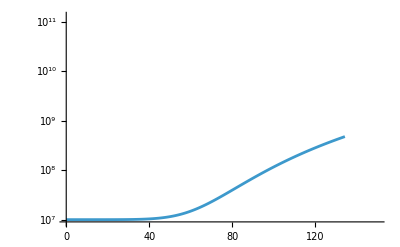

```mathematica
ListLinePlot[Transpose[{sigma,eqn6-eqn6[[1]]+1 10^7}],PlotRange->{{0,150},{9. 10^6,13000.651 10^7}},ScalingFunctions->{Automatic,"Log"}]
```

```mathematica
lam1=440^2;
lam2=5;
lam3=3.33123*10^-72;
Plot[lam1 rho+lam2/2 rho^2+lam3 rho^20,{rho,0,45000},PlotRange->All]
```

-Graphics-